Series

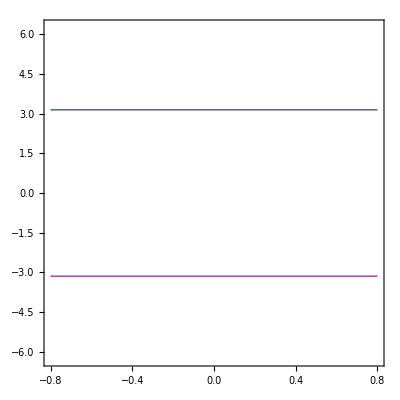

```mathematica
d1=0.1;
d2=0.5;
t=0.4;
Series
f1[n_,x_,z_]:=√(n*x^2+(d1^2+d2^2-2*d1*d2*Cos[z]));
f2[x_,z_]:=√(x^2+t^2*(Cos[z])^2)+t*Cos[z];
f3[n_,x_,z_]:=n*x-t*Cos[z];
Manipulate[Plot[{f1[1,x,z],f1[2,x,z],f1[3,x,z],f1[4,x,z],0.6},{z,-Pi,Pi}],{x,0,1}]
Manipulate[Plot[{f3[1,x,z],f3[2,x,z],f3[3,x,z],f3[4,x,z],1},{z,-Pi,Pi}],{x,0,1}]
ContourPlot [{f1[x,z]==0.6,f1[x,z]==0.5,f1[x,z]==0.41,f1[x,z]==0.8,z==Pi,z==-Pi},{x,-0.8,0.8},{z,-2*Pi,2*Pi}]
```

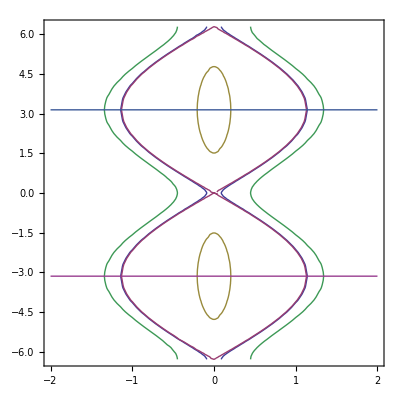

```mathematica
ContourPlot [{f2[x,z]==0.81,f2[x,z]==0.8,f2[x,z]==0.05,f2[x,z]==1,z==Pi,z==-Pi},{x,-2,2},{z,-2*Pi,2*Pi}]
```

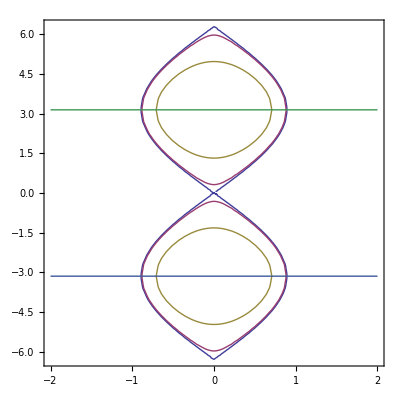

```mathematica
ContourPlot [{f3[x,z]==0.4,f3[x,z]==0.38,f3[x,z]==0.1,z==Pi,z==-Pi},{x,-2,2},{z,-2*Pi,2*Pi}]
```